```mathematica
Quit[];
```

Intro (*)

We introduce the following notation for 1- and 2-point scalar and tensor integrals

	A_o[m] = ∫[d^dk] 1/d_1[m]
	
	B_0[q,m1,m2] = ∫[d^dk] 1/(d_1[m1]d_2[m2])
	
	B^μ[q,m1,m2] = ∫[d^dk] k^μ/(d_1[m1]d_2[m2])= q^μ B_1
	
	B^(μ⋁)[q,m1,m2] = ∫[d^dk] (k^μ k^ν)/(d_1[m1]d_2[m2])= B_00 g^μν+B_11 q^μ q^ν
	
where the denominators read

	d_1[m] = k^2-m^2
	d_2[m] = (k+q)^2-m^2

```mathematica
<<PVReduction`
```

PVReduction package by Sebastian Sapeta, 2017

```mathematica
ReplNumerators=Flatten[{GenNumReplacements[d2,(q+k)^2-m2^2]}]
```

{sp[k,q]→1/2 (m2^2+d2[m2]-sp[k,k]-sp[q,q])}

### Scalar integrals

Bubble [Smirnov (3.5)]. Factor (2π)^-d from the measure included already before.

```mathematica
bubint=I Pi^(d/2)Gamma[ep] 1/((m^2-q^2 xi(1-xi))^ep)/.m-> 0
```

ⅈ π^(d/2) (-q^2 (1-xi) xi)^-ep Gamma[ep]

```mathematica
intres=Integrate[bubint,{xi,0,1}]
```

ConditionalExpression[(ⅈ π^(d/2) (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/Gamma[2-2 ep],Re[ep]<1]

```mathematica
bubble[q_]=intres[[1]]
```

(ⅈ π^(d/2) (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/Gamma[2-2 ep]

Passarino-Veltman reduction - general case (*)

List of tensors to be analyzed:

```mathematica
T0:=1/(d1[m1]d2[m2])
T[mu_]:=k[mu]/(d1[m1]d2[m2])
T[mu_,nu_]:=(k[mu]k[nu])/(d1[m1]d2[m2])
```

### B^μ

```mathematica
ineq1=T[mu]-q[mu]B1;
eq1=ContractReplNumWrapShift[ineq1,q[mu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

1/2 (A0[m1]-A0[m2]-2 B1 q.q-B0[m1,m2] (m1^2-m2^2+q.q))

```mathematica
sol1=Flatten[Solve[eq1==0,B1]]//FullSimplify
```

{B1→-(-A0[m1]+A0[m2]+B0[m1,m2] (m1^2-m2^2+q.q))/(2 q.q)}

### B^μν

```mathematica
ineq2=T[mu,nu]-(g[mu,nu]B00+q[mu]q[nu]B11);
```

Contraction with q^μ

```mathematica
eq2nu=ContractReplNumWrapShift[ineq2,q[mu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

1/2 (-2 B00-B1 m1^2+B1 m2^2+A0[m2]-(B1+2 B11) q.q) q[nu]

```mathematica
eq21=ContractReplNumWrapShift[eq2nu,q[nu],ReplNumerators]//FullSimplify
```

1/2 q.q (-2 B00-B1 m1^2+B1 m2^2+A0[m2]-(B1+2 B11) q.q)

Contraction with g^μν

```mathematica
eq22=ContractReplNumWrapShift[ineq2,g[mu,nu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

-B00 d+A0[m2]+m1^2 B0[m1,m2]-B11 q.q

```mathematica
sol2=Flatten[Solve[{eq21==0,eq22==0},{B11,B00}]]//FullSimplify
```

{B11→((-2+d) A0[m2]-2 m1^2 B0[m1,m2]-B1 d (m1^2-m2^2+q.q))/(2 (-1+d) q.q),B00→(A0[m2]+2 m1^2 B0[m1,m2]+B1 (m1^2-m2^2+q.q))/(2 (-1+d))}

### Comparison with Ellis et al. PR 518 (2012) 141

```mathematica
B1ref=1/(2 q.q)(f1 B0[m1,m2]+A0[m1]-A0[m2]);
B11ref=1/(2 q.q)(f1 B1+A0[m2]-2B00);
B00ref=1/(2 (d-1))(2 m1^2 B0[m1,m2]+A0[m2]-f1 B1);
f1=m2^2-m1^2-q.q;
```

```mathematica
B1ref==B1/.sol1//Simplify
B00ref==B00/.sol2//Simplify
B11ref==B11/.sol2//Simplify
```

True

True

True

Vacuum polarization: Π_qq

## Tensor integral

```mathematica
ReplTrSum={
tr[args1___,a1_+a2_,args2___]-> tr[args1,a1,args2]+ tr[args1,a2,args2]
};
ReplTrFac={
tr[args1___,(mass:m1|m2)^(n_.),args2___]-> mass^n tr[args1,args2],
tr[args1___,-gamma[arg1_](v:k|q)[arg2_],args2___]->-tr[args1,gamma[arg1],args2]v[arg2],tr[args1___,gamma[arg1_](v:k|q)[arg2_],args2___]->tr[args1,gamma[arg1],args2]v[arg2],
tr[args1___,-gamma[arg1_],args2___]->-tr[args1,gamma[arg1],args2]
};
ReplTr={
tr[gamma[a_],gamma[b_]]-> 4g[a,b],
tr[gamma[a_],gamma[b_],gamma[c_]]-> 0,
tr[gamma[a_],gamma[b_],gamma[c_],gamma[d_]]-> 4(g[a,b]g[c,d]-g[a,c]g[b,d]+g[a,d]g[b,c])
};
```

In case of (-k, q-k), or equivalently (k,k-q) momenta in the loop the numerator of the vacuum polarization integral reads

```mathematica
gammaprod=tr[gamma[mu],q[sigma]gamma[sigma]-k[sigma]gamma[sigma]+m1,gamma[nu],-k[rho]gamma[rho]+m2];
```

```mathematica
Expand[gammaprod//.ReplTrSum//.ReplTrFac/.ReplTr]//.ReplContractions
```

4 m1 m2 g[mu,nu]+8 k[mu] k[nu]-4 k[nu] q[mu]-4 k[mu] q[nu]-4 g[mu,nu] sp[k,k]+4 g[mu,nu] sp[k,q]

In the case (k,q+k) momenta in the loop, as in the DKS book, we have

```mathematica
gammaprod=tr[gamma[mu],k[sigma]gamma[sigma]+q[sigma]gamma[sigma]+m1,gamma[nu],k[rho]gamma[rho]+m2];
```

```mathematica
numerator=Expand[gammaprod//.ReplTrSum//.ReplTrFac/.ReplTr]//.ReplContractions
```

4 m1 m2 g[mu,nu]+8 k[mu] k[nu]+4 k[nu] q[mu]+4 k[mu] q[nu]-4 g[mu,nu] sp[k,k]-4 g[mu,nu] sp[k,q]

The two above numerators can be turned into each other via k -> -k transformation.

List with prefactors appearing at various stages

```mathematica
prefac={};
```

```mathematica
(* fermion loop, vertex factors, I^2 from propagators, 1-loop integration measure *)
AppendTo[prefac,{-1,(-I g)^2,I^2 1/(2Pi)^d}]
```

{{-1,-g^2,-(2 π)^-d}}

```mathematica
T[mu_,nu_]=numerator/(d1[m1]d2[m2])
```

(4 m1 m2 g[mu,nu]+8 k[mu] k[nu]+4 k[nu] q[mu]+4 k[mu] q[nu]-4 g[mu,nu] sp[k,k]-4 g[mu,nu] sp[k,q])/(d1[m1] d2[m2])

## PV reduction

```mathematica
ineq2=T[mu,nu]-(g[mu,nu]T00+q[mu]q[nu]T11);
```

Contraction with q^μ

```mathematica
eq2nu=ContractReplNumWrapShift[ineq2,q[mu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

-(4 B1 (m1-m2) (m1+m2)+T00+4 m1 (m1-m2) B0[m1,m2]+T11 q.q) q[nu]

```mathematica
eq21=ContractReplNumWrapShift[eq2nu,q[nu],ReplNumerators]//FullSimplify
```

-q.q (4 B1 (m1-m2) (m1+m2)+T00+4 m1 (m1-m2) B0[m1,m2]+T11 q.q)

Contraction with g^μν

```mathematica
eq22=ContractReplNumWrapShift[ineq2,g[mu,nu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

FullSimplx`ify[-d T00+4 A0[m1]-2 d A0[m1]+4 A0[m2]-2 d A0[m2]+4 m1^2 B0[m1,m2]-2 d m1^2 B0[m1,m2]+4 d m1 m2 B0[m1,m2]+4 m2^2 B0[m1,m2]-2 d m2^2 B0[m1,m2]-T11 q.q-4 B0[m1,m2] q.q+2 d B0[m1,m2] q.q]

```mathematica
sol2=Flatten[Solve[{eq21==0,eq22==0},{T11,T00}]]/.sol1//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{T11→1/((-1+d) (q.q)^2)(2 d (m1-m2) (m1+m2) (-A0[m1]+A0[m2]+(m1-m2) (m1+m2) B0[m1,m2])+2 ((-2+d) (A0[m1]+A0[m2])-2 (m1^2+m2^2) B0[m1,m2]) q.q-2 (-2+d) B0[m1,m2] (q.q)^2+q.q (FullSimplx`ify)^(-1)[0]),T00→-1/((-1+d) q.q)(2 A0[m2] (m1^2-m2^2+(-2+d) q.q)+2 A0[m1] (-m1^2+m2^2+(-2+d) q.q)+2 B0[m1,m2] ((m1-m2)^2-q.q) ((m1+m2)^2+(-2+d) q.q)+q.q (FullSimplx`ify)^(-1)[0])}

```mathematica
Cases[sol2,A0[_]|B0[_,_],-1]//DeleteDuplicates
```

{A0[m1],A0[m2],B0[m1,m2]}

## Specific case with m_1 = m_2 = m

In our case of massive bubble with m1=m2, we get the following coefficient

```mathematica
ReplFinal={m1-> m,m2-> m,d-> 4-2ep};
coeff00=T00/.sol2/.ReplFinal//Simplify
coeff11=T11/.sol2/.ReplFinal//Simplify
```

(-8 (-1+ep) A0[m]-4 B0[m,m] (2 m^2+q.q-ep q.q)+(FullSimplx`ify)^(-1)[0])/(-3+2 ep)

(8 (-1+ep) A0[m]+4 B0[m,m] (2 m^2+q.q-ep q.q)-(FullSimplx`ify)^(-1)[0])/((-3+2 ep) q.q)

We see already at this stage that the coefficients are identical up to the q.q prefactor.

### Scalar integrals

```mathematica
(* MSbar renormalization *)
AppendTo[prefac,Exp[EulerGamma ep]mu^(2ep)/(4Pi)^ep]
```

{{-1,-g^2,-(2 π)^-d},ⅇ^(ep EulerGamma) mu^(2 ep) (4 π)^-ep}

One point [Smirnov (A.1); agrees with OY (2.36)]. Factor (2π)^-d from the measure included already before.

```mathematica
tadpole[m_]:= -I Pi^(d/2)Gamma[-1+ep](m^2)^(1-ep)//Simplify
```

Bubble [Smirnov (3.5)]. Factor (2π)^-d from the measure included already before.

```mathematica
bubint=I Pi^(d/2)Gamma[ep] 1/((m^2-q^2 xi(1-xi))^ep)/.q^2-> 4 r m^2
```

ⅈ π^(d/2) (m^2-4 m^2 r (1-xi) xi)^-ep Gamma[ep]

```mathematica
bubint//Factor
```

ⅈ π^(d/2) (m^2-4 m^2 r (1-xi) xi)^-ep Gamma[ep]

Because the 1/()^eppart is finite we can expand it under the integral

```mathematica
bublist = Simplify[bubint]/.{fac_ Power[m^2 arg_,-ep]-> {m^(-2ep)fac,arg^-ep}}
bubint2=Series[bublist[[2]],{ep,0,1}]//Simplify//Normal
```

{ⅈ m^(-2 ep) π^(d/2) Gamma[ep],(1+4 r (-1+xi) xi)^-ep}

1-ep Log[1+4 r (-1+xi) xi]

```mathematica
intres=Integrate[bubint2,{xi,0,1}]
```

ConditionalExpression[1-ep (-2+(2 √(1-r) ArcTan[(√r)/(√(1-r))])/(√r)),((√((-1+r) r))/r∉Reals||Re[(√((-1+r) r))/r]<-1||Re[(√((-1+r) r))/r]>1)&&(Re[(√(1-r))/(√r)]≠0||Im[(√(1-r))/(√r)]<-1||Im[(√(1-r))/(√r)]>1)]

```mathematica
bubble[r_,m_]=bublist[[1]]intres[[1]]
```

ⅈ m^(-2 ep) π^(d/2) (1-ep (-2+(2 √(1-r) ArcTan[(√r)/(√(1-r))])/(√r))) Gamma[ep]

```mathematica
AppendTo[prefac,ⅈ (m^-2)^ep π^(d/2)]
```

{{-1,-g^2,-(2 π)^-d},ⅇ^(ep EulerGamma) mu^(2 ep) (4 π)^-ep,ⅈ (1/m^2)^ep π^(d/2)}

```mathematica
tad=tadpole[m]/(ⅈ (m^2)^-ep π^(d/2))
bub=bubble[r,m]/(ⅈ m^(-2ep) π^(d/2))
```

-m^2 Gamma[-1+ep]

(1-ep (-2+(2 √(1-r) ArcTan[(√r)/(√(1-r))])/(√r))) Gamma[ep]

Relation from Wikipedia. Valid in the range where the functions are real and single-valued.

```mathematica
FullSimplify[x/Sqrt[x^2+1]/.x-> (√r)/(√(1-r)),Assumptions->{r>0,r<1}]
```

√r

```mathematica
bub=bub/.ArcTan[__]-> ArcSin[Sqrt[r]]
```

(1-ep (-2+(2 √(1-r) ArcSin[√r])/(√r))) Gamma[ep]

### Final result for r<1

```mathematica
coeff11
```

(8 (-1+ep) A0[m]+4 B0[m,m] (2 m^2+q.q-ep q.q)-(FullSimplx`ify)^(-1)[0])/((-3+2 ep) q.q)

```mathematica
ff=Collect[Series[coeff11/.q.q-> 4 m^2 r/.{A0[m]-> tad,B0[m,m]-> bub},{ep,0,0}]//Normal,ep,Apart]
```

-4/(3 ep)+(4 EulerGamma)/3+(4 √(1-r) ArcSin[√r])/(3 r^(3/2))+(8 √(1-r) ArcSin[√r])/(3 √r)-(48 m^2+80 m^2 r-3 (FullSimplx`ify)^(-1)[0])/(36 m^2 r)

```mathematica
Flatten[prefac]
```

{-1,-g^2,-(2 π)^-d,ⅇ^(ep EulerGamma) mu^(2 ep) (4 π)^-ep,ⅈ (1/m^2)^ep π^(d/2)}

```mathematica
gfac=Times@@(Flatten[prefac])
```

-ⅈ 2^(-d-2 ep) ⅇ^(ep EulerGamma) g^2 (1/m^2)^ep mu^(2 ep) π^(-d/2-ep)

```mathematica
gfac/.d-> 4-2ep//PowerExpand//FullSimplify
```

-(ⅈ ⅇ^(ep EulerGamma) g^2 m^(-2 ep) mu^(2 ep))/(16 π^2)

```mathematica
f1=Series[gfac/.d-> 4-2ep,{ep,0,1}]
```

-(ⅈ g^2)/(16 π^2)-(ⅈ g^2 (EulerGamma+Log[1/m^2]+2 Log[mu]) ep)/(16 π^2)+O[ep]^2

```mathematica
fac=(I g^2)/(12 Pi^2);
tmp=Collect[f1 ff/fac//Normal,ep,Apart];
tmp=Collect[tmp,r,Simplify]/.{fac1_ ArcSin[arg_]+fac2_ ArcSin[arg_]:>  FullSimplify[fac1+fac2]ArcSin[arg]};
tmp=tmp/.{fac1_. Log[arg1_]+fac2_. Log[arg2_]:>  FullSimplify[fac1 Log[arg1]+fac2 Log[arg2],Assumptions->{m>0,mu>0}]};
res01=fac tmp/. g^2-> α 4 Pi
```

(ⅈ α (5/3+1/ep-(√(1-r) (1+2 r) ArcSin[√r])/r^(3/2)+Log[mu^2/m^2]+(1-((FullSimplx`ify)^(-1)[0])/(16 m^2))/r))/(3 π)

### Analytic continuation to r>1

We have two functions which become complex-valued when r>1: √(1-r) and ArcSin[√r]. We know that our prescription corresponds to s + iϵ, hence we should perform the analytic continuation via the upper half plane.

#### The case of √(1-r)

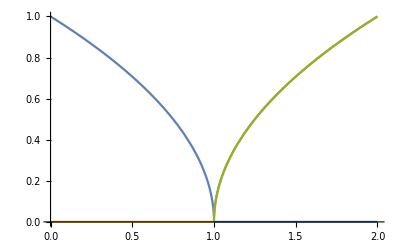

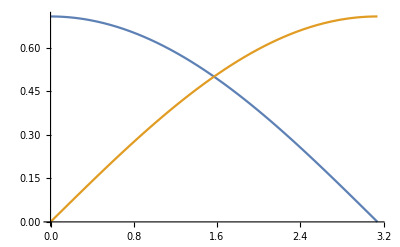

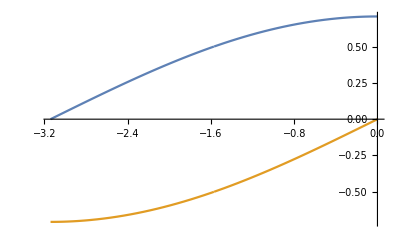

```mathematica
f[r_]:=Sqrt[1-r]
g[phi_]:=Sqrt[tau]/.tau->1/2 Exp[I phi]
Plot[{Re[f[r]],Im[f[r]],Sqrt[r-1]},{r,0,2}]
Plot[{Re[g[phi]],Im[g[phi]]},{phi,0,Pi}]
Plot[{Re[g[phi]],Im[g[phi]]},{phi,0,-Pi}]
```

#### The case of ArcSin[√r]

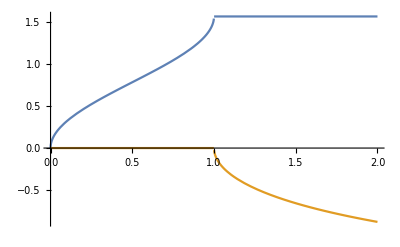

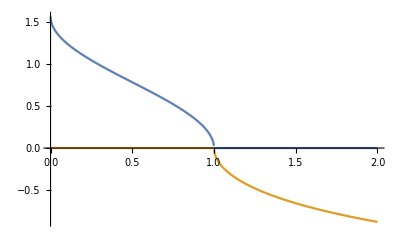

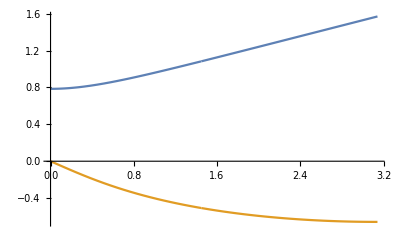

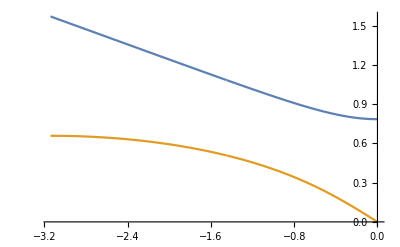

```mathematica
f[r_]:=ArcSin[Sqrt[r]]
h[r_]:= -I Log[Sqrt[r]+Sqrt[r-1]]
g[phi_]:=ArcSin[Sqrt[1-tau]]/.tau->1/2 Exp[I phi]
Plot[{Re[f[r]],Im[f[r]]},{r,0,2}]
Plot[{Re[h[r]],Im[h[r]]},{r,0,2}]
Plot[{Re[g[phi]],Im[g[phi]]},{phi,0,Pi}]
Plot[{Re[g[phi]],Im[g[phi]]},{phi,0,-Pi}]
```

What counts in fact is the real part of ArcSin[√r] as  the √(1-r)function is purely imaginary. Therefore, for the imaginary part of the amplitude we get:

```mathematica
1/I res01/.{Sqrt[1-r]-> cI Sqrt[r-1],ArcSin[√r]-> Pi/2}
```

(α (5/3+1/ep-(cI π √(-1+r) (1+2 r))/(2 r^(3/2))+Log[mu^2/m^2]+(1-((FullSimplx`ify)^(-1)[0])/(16 m^2))/r))/(3 π)

```mathematica
resg1=Plus@@Cases[Expand[1/I res01/.{Sqrt[1-r]-> cI Sqrt[r-1],ArcSin[√r]-> Pi/2}],cI func_-> func,-1]//Simplify
```

-(√(-1+r) (1+2 r) α)/(6 r^(3/2))

And this agrees with YO, Eq. (3.23).

## Specific case with m_1 = m_2 = 0

In our case of massive bubble with m1=m2, we get the following coefficient

```mathematica
ReplFinal={m1-> 0,m2-> 0,d-> 4-2ep};
coeff00=T00/.sol2/.ReplFinal//Simplify
coeff11=T11/.sol2/.ReplFinal//Simplify
```

(-8 (-1+ep) A0[0]+4 (-1+ep) B0[0,0] q.q+(FullSimplx`ify)^(-1)[0])/(-3+2 ep)

-(-8 (-1+ep) A0[0]+4 (-1+ep) B0[0,0] q.q+(FullSimplx`ify)^(-1)[0])/((-3+2 ep) q.q)

We see already at this stage that the coefficients are identical up to the q.q prefactor.

### Scalar integrals

Bubble [Smirnov (3.5)]. Factor (2π)^-d from the measure included already before.

```mathematica
bubint=I Pi^(d/2)Gamma[ep] 1/((m^2-q^2 xi(1-xi))^ep)/.m-> 0
```

ⅈ π^(d/2) (-q^2 (1-xi) xi)^-ep Gamma[ep]

```mathematica
intres=Integrate[bubint,{xi,0,1}]
```

ConditionalExpression[(ⅈ π^(d/2) (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/Gamma[2-2 ep],Re[ep]<1]

```mathematica
bubble[q_]=intres[[1]]
```

(ⅈ π^(d/2) (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/Gamma[2-2 ep]

### Final result

```mathematica
fexact=coeff11/.q.q-> 4 m^2 r/.{A0[0]-> 0,B0[0,0]-> bubble[q]}/.d-> 4-2ep//Simplify
```

-((16 ⅈ (-1+ep) m^2 π^(2-ep) (-q^2)^-ep r Gamma[1-ep]^2 Gamma[ep])/Gamma[2-2 ep]+(FullSimplx`ify)^(-1)[0])/(4 (-3+2 ep) m^2 r)

```mathematica
fapprox=Collect[Series[fexact,{ep,0,0}]//Normal,ep,Apart]
```

-(4 ⅈ π^2)/(3 ep)+4/9 ⅈ π^2 (-5+3 EulerGamma+3 Log[π]+3 Log[-q^2])+((FullSimplx`ify)^(-1)[0])/(12 m^2 r)

```mathematica
Flatten[Delete[prefac,-1]]
```

{-1,-g^2,-(2 π)^-d,ⅇ^(ep EulerGamma) mu^(2 ep) (4 π)^-ep}

```mathematica
prefacexact=Times@@(Flatten[Delete[prefac,-1]])/.d-> 4-2ep
```

-1/16 ⅇ^(ep EulerGamma) g^2 mu^(2 ep) π^(-4+ep)

```mathematica
prefacapprox=Series[prefacexact,{ep,0,1}]
```

-g^2/(16 π^4)+((-EulerGamma g^2-2 g^2 Log[mu]-g^2 Log[π]) ep)/(16 π^4)+O[ep]^2

```mathematica
resexact =Series[prefacexact fexact,{ep,0,0}]/. 6 Log[mu]-3 Log[-q^2]-> 3Log[mu^2/-q^2]
```

(ⅈ g^2)/(12 π^2 ep)+(ⅈ g^2 (80 m^2 π^2 r+96 m^2 π^2 r Log[mu]-48 m^2 π^2 r Log[-q^2]+3 ⅈ (FullSimplx`ify)^(-1)[0]))/(576 m^2 π^4 r)+O[ep]^1

```mathematica
resapprox=Simplify[prefacapprox fapprox]/. 6 Log[mu]-3 Log[-q^2]-> 3Log[mu^2/-q^2]
```

(ⅈ g^2)/(12 π^2 ep)+(ⅈ g^2 (80 m^2 π^2 r+96 m^2 π^2 r Log[mu]-48 m^2 π^2 r Log[-q^2]+3 ⅈ (FullSimplx`ify)^(-1)[0]))/(576 m^2 π^4 r)+O[ep]^1

```mathematica
fac=(I g^2)/(12 Pi^2);
tmp=Collect[resapprox/fac//Normal,ep,Apart];
resm0=fac tmp/. g^2-> α 4 Pi
```

(ⅈ α (1/ep+1/3 (5+6 Log[mu]-3 Log[-q^2])+(ⅈ (FullSimplx`ify)^(-1)[0])/(16 m^2 π^2 r)))/(3 π)

```mathematica
res01
```

(ⅈ α (5/3+1/ep-(√(1-r) (1+2 r) ArcSin[√r])/r^(3/2)+Log[mu^2/m^2]+(1-((FullSimplx`ify)^(-1)[0])/(16 m^2))/r))/(3 π)

```mathematica
tmp=FullSimplify[1/I res01/.1/r-(√(1-r) (1+2 r) ArcSin[√r])/r^(3/2)-> -2I(Pi/2-I Log[2 Sqrt[r]])/.r-> q^2/(4 m^2),Assumptions->{m>0}];
Collect[tmp/. 3 ep Log[mu^2]-3 ep Log[q^2]-> 3ep Log[m^2/q^2],ep,Apart]
```

α/(3 ep π)-(4 m^2 √(4 m^2-q^2) α ArcCsc[(2 m)/q])/(3 π q^3)-(2 √(4 m^2-q^2) α ArcCsc[(2 m)/q])/(3 π q)+(α Log[-(ⅈ mu)/m^2])/(3 π)+(α (48 m^2+20 q^2+12 q^2 Log[ⅈ mu]-3 (FullSimplx`ify)^(-1)[0]))/(36 π q^2)

```mathematica
Log[-1]
```

ⅈ π

Vacuum polarization: Π_gg+ Π_ηη

## Common

```mathematica
ReplDep={1/ep-> Dep-Log[4Pi]+EulerGamma};
```

Prefactors

```mathematica
(* colour, vertex, symmetry, 1-loop integration measure, MSbar renormalization *)
prefacDKSgg={CA ,(-g)^2,1/2,1/(2Pi)^d,mu^(2ep)};
prefacexactDKSgg=Times@@(Flatten[prefacDKSgg])/.d-> 4-2ep

(* colour, vertex, fermion loop, 1-loop integration measure, MSbar renormalization *)
prefacDKSee={CA ,(-g)^2,-1,1/(2Pi)^d,mu^(2ep)};
prefacexactDKSee=Times@@(Flatten[prefacDKSee])/.d-> 4-2ep
```

2^(-5+2 ep) CA g^2 mu^(2 ep) π^(-4+2 ep)

-CA g^2 mu^(2 ep) (2 π)^(-4+2 ep)

```mathematica
newfac=α/(4Pi)CA 1/12;
```

## Tensor integralΠ_gg

In case of (-k, q-k), or equivalently (k,k-q) momenta in the loop the numerator of the vacuum polarization integral reads

```mathematica
(*numprod=tgv[a,mu,q,b1,n1,-q+k,c1,s1,-k]g[n1,m2] tgv[a2,m2,q-k,b,nu,-q,c2,s2,k]g[s1,s2]
numerator=Collect[Expand[numprod]//.ReplContractions,{k[mu] q[nu], k[nu] q[mu], k[mu] q[nu],q[mu]q[nu],g[_,_]},Simplify]*)
```

In the case (k,q+k) momenta in the loop, as in the DKS book, we have

```mathematica
tgvF[mu,q,ap,-q-k,be,k]//Simplify
tgvF[ga,q+k,nu,-q,de,-k]//Simplify
numprod=tgvF[mu,q,ap,-q-k,be,k]g[ap,ga] tgvF[ga,q+k,nu,-q,de,-k]g[be,de]
numerator=Collect[Expand[numprod]//.ReplContractions,{k[mu] q[nu], k[nu] q[mu], k[mu] q[nu],q[mu]q[nu],g[_,_]},Simplify]
```

g[be,mu] (k[ap]-q[ap])+g[mu,ap] (k[be]+2 q[be])-g[ap,be] (2 k[mu]+q[mu])

g[ga,nu] (k[de]+2 q[de])+g[nu,de] (k[ga]-q[ga])-g[de,ga] (2 k[nu]+q[nu])

g[ap,ga] g[be,de] (g[be,mu] (k[ap]-q[ap])+g[mu,ap] (k[be]+2 q[be])+g[ap,be] (-2 k[mu]-q[mu])) (g[ga,nu] (k[de]+2 q[de])+g[nu,de] (k[ga]-q[ga])+g[de,ga] (-2 k[nu]-q[nu]))

2 (-3+2 d) k[mu] k[nu]+(-3+2 d) k[nu] q[mu]+(-3+2 d) k[mu] q[nu]+(-6+d) q[mu] q[nu]+g[nu,mu] (sp[k,k]-2 sp[k,q]+sp[q,q])+g[mu,nu] (sp[k,k]+4 (sp[k,q]+sp[q,q]))

```mathematica
T[mu_,nu_]=numerator/(d1[m1]d2[m2])
```

1/(d1[m1] d2[m2])(2 (-3+2 d) k[mu] k[nu]+(-3+2 d) k[nu] q[mu]+(-3+2 d) k[mu] q[nu]+(-6+d) q[mu] q[nu]+g[nu,mu] (sp[k,k]-2 sp[k,q]+sp[q,q])+g[mu,nu] (sp[k,k]+4 (sp[k,q]+sp[q,q])))

## PV reduction Π_gg

```mathematica
ineq2=T[mu,nu]-(g[mu,nu]T00+q[mu]q[nu]T11);
```

Contraction with q^μ

```mathematica
eq2nu=ContractReplNumWrapShift[ineq2,q[mu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

-1/2 ((1-2 d) A0[m1]+(1-2 d) A0[m2]+B0[m1,m2] ((-5+2 d) m1^2+m2^2-2 d m2^2+q.q)+2 (B1 (-3+2 d) (m1-m2) (m1+m2)+T00+T11 q.q)) q[nu]

```mathematica
eq21=ContractReplNumWrapShift[eq2nu,q[nu],ReplNumerators]//FullSimplify
```

-1/2 q.q ((1-2 d) A0[m1]+(1-2 d) A0[m2]+B0[m1,m2] ((-5+2 d) m1^2+m2^2-2 d m2^2+q.q)+2 (B1 (-3+2 d) (m1-m2) (m1+m2)+T00+T11 q.q))

Contraction with g^μν

```mathematica
eq22=ContractReplNumWrapShift[ineq2,g[mu,nu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

-d T00+3 (-1+d) A0[m1]+3 (-1+d) A0[m2]-T11 q.q+3 (-1+d) B0[m1,m2] (m1^2+m2^2+q.q)

```mathematica
sol2=Flatten[Solve[{eq21==0,eq22==0},{T11,T00}]]/.sol1/.{m1-> 0,m2-> 0}//FullSimplify
```

{T11→(2 (-2+d) (-3+2 d) A0[0]+(6-7 d) B0[0,0] q.q)/(2 (-1+d) q.q),T00→(2 (-5+4 d) A0[0]+(-5+6 d) B0[0,0] q.q)/(2 (-1+d))}

## Final transformations Π_gg

In our case of massive bubble with m1=m2, we get the following coefficient

```mathematica
ReplFinal={d-> 4-2ep,q.q-> q^2};
coeff00=T00/.sol2/.ReplFinal//Simplify
coeff11=T11/.sol2/.ReplFinal//Simplify
```

(2 (-11+8 ep) A0[0]+(-19+12 ep) q^2 B0[0,0])/(-6+4 ep)

(-2 (5-9 ep+4 ep^2) A0[0]+(11-7 ep) q^2 B0[0,0])/((-3+2 ep) q^2)

We see already that, unlike in the quark case, here the coefficients are not identical. This is because we are still missing ghosts.

### Final result

```mathematica
fexact11gg=coeff11/.{A0[0]-> 0,B0[0,0]-> bubble[q]}/.ReplFinal//Simplify
fexact00gg=coeff00/.{A0[0]-> 0,B0[0,0]-> bubble[q]}/.ReplFinal//Simplify
```

-(ⅈ (-11+7 ep) π^(2-ep) (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/((-3+2 ep) Gamma[2-2 ep])

(ⅈ (-19+12 ep) π^(2-ep) q^2 (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/(2 (-3+2 ep) Gamma[2-2 ep])

```mathematica
resggDKS =Series[prefacexactDKSgg {fexact11gg,fexact00gg},{ep,0,0}]//Normal
```

{-(11 ⅈ CA g^2)/(96 ep π^2)+(ⅈ (-67 CA g^2+33 CA EulerGamma g^2-66 CA g^2 Log[2]-66 CA g^2 Log[mu]-33 CA g^2 Log[π]+33 CA g^2 Log[-q^2]))/(288 π^2),(19 ⅈ CA g^2 q^2)/(192 ep π^2)-(ⅈ (-116 CA g^2 q^2+57 CA EulerGamma g^2 q^2-114 CA g^2 q^2 Log[2]-114 CA g^2 q^2 Log[mu]-57 CA g^2 q^2 Log[π]+57 CA g^2 q^2 Log[-q^2]))/(576 π^2)}

```mathematica
tmp=resggDKS/.ReplDep/. g^2-> α 4 Pi/.Log[-q^2]-> 2 Log[mu]+ Log[-q^2/mu^2]//Simplify;
tmp=tmp/newfac//Expand;
Pigg=Collect[(tmp[[2]] g[mu,nu] + tmp[[1]] q[mu]q[nu]),{q[mu] q[nu],g[mu,nu]},Simplify]
```

1/3 ⅈ q^2 g[mu,nu] (116+57 Dep-57 Log[-q^2/mu^2])-2/3 ⅈ (67+33 Dep-33 Log[-q^2/mu^2]) q[mu] q[nu]

## Tensor integralΠ_ηη

In the case (k,q+k) momenta in the loop, as in the DKS book, we have

```mathematica
numerator=(k[mu]+q[mu])k[nu]
```

k[nu] (k[mu]+q[mu])

```mathematica
T[mu_,nu_]=numerator/(d1[m1]d2[m2])
```

(k[nu] (k[mu]+q[mu]))/(d1[m1] d2[m2])

## PV reduction Π_ηη

```mathematica
ineq2=T[mu,nu]-(g[mu,nu]T00+q[mu]q[nu]T11);
```

Contraction with q^μ

```mathematica
eq2nu=ContractReplNumWrapShift[ineq2,q[mu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

1/2 (-B1 m1^2+B1 m2^2-2 T00+A0[m2]+(B1-2 T11) q.q) q[nu]

```mathematica
eq21=ContractReplNumWrapShift[eq2nu,q[nu],ReplNumerators]//FullSimplify
```

1/2 q.q (-B1 m1^2+B1 m2^2-2 T00+A0[m2]+(B1-2 T11) q.q)

Contraction with g^μν

```mathematica
eq22=ContractReplNumWrapShift[ineq2,g[mu,nu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

1/2 (A0[m1]+A0[m2]+B0[m1,m2] (m1^2+m2^2-q.q)-2 (d T00+T11 q.q))

```mathematica
sol2=Flatten[Solve[{eq21==0,eq22==0},{T11,T00}]]/.sol1/.{m1-> 0,m2-> 0}//FullSimplify
```

{T11→-((-2+d) (-2 A0[0]+B0[0,0] q.q))/(4 (-1+d) q.q),T00→(2 A0[0]-B0[0,0] q.q)/(4 (-1+d))}

## Final transformations Π_ηη

```mathematica
ReplFinal={d-> 4-2ep,q.q-> q^2};
coeff11=T11/.sol2/.ReplFinal//Simplify
coeff00=T00/.sol2/.ReplFinal//Simplify
```

-((-1+ep) (-2 A0[0]+q^2 B0[0,0]))/(2 (-3+2 ep) q^2)

(-2 A0[0]+q^2 B0[0,0])/(-12+8 ep)

### Final result

```mathematica
fexact11ee=coeff11/.{A0[0]-> 0,B0[0,0]-> bubble[q]}/.ReplFinal//Simplify
fexact00ee=coeff00/.{A0[0]-> 0,B0[0,0]-> bubble[q]}/.ReplFinal//Simplify
```

-(ⅈ (-1+ep) π^(2-ep) (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/(2 (-3+2 ep) Gamma[2-2 ep])

(ⅈ π^(2-ep) q^2 (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/(4 (-3+2 ep) Gamma[2-2 ep])

```mathematica
reseeDKS =Series[prefacexactDKSee {fexact11ee,fexact00ee},{ep,0,0}]//Normal
```

{(ⅈ CA g^2)/(96 ep π^2)-(ⅈ (-5 CA g^2+3 CA EulerGamma g^2-6 CA g^2 Log[2]-6 CA g^2 Log[mu]-3 CA g^2 Log[π]+3 CA g^2 Log[-q^2]))/(288 π^2),(ⅈ CA g^2 q^2)/(192 ep π^2)-(ⅈ CA g^2 q^2 (-8+3 EulerGamma-6 Log[2]-6 Log[mu]-3 Log[π]+3 Log[-q^2]))/(576 π^2)}

```mathematica
tmp=reseeDKS/.ReplDep/. g^2-> α 4 Pi/.Log[-q^2]-> 2 Log[mu]+ Log[-q^2/mu^2]//Simplify;
tmp=tmp/newfac//Expand;
Piee=Collect[(tmp[[2]] g[mu,nu] + tmp[[1]] q[mu]q[nu]),{q[mu] q[nu],g[mu,nu]},Simplify]
```

1/3 ⅈ q^2 g[mu,nu] (8+3 Dep-3 Log[-q^2/mu^2])+2/3 ⅈ (5+3 Dep-3 Log[-q^2/mu^2]) q[mu] q[nu]

## Π_gg+Π_ηη

```mathematica
Collect[Pigg+Piee,{ q[mu] q[nu],g[mu,nu]},FullSimplify]
```

4/3 ⅈ q^2 g[mu,nu] (31+15 Dep-15 Log[-q^2/mu^2])-4/3 ⅈ (31+15 Dep-15 Log[-q^2/mu^2]) q[mu] q[nu]

```mathematica
fac=ⅈ CA α/(4Pi);
Pigauge=C[fac]newfac Factor[(Pigg+Piee)/fac]
```

1/9 C[(ⅈ CA α)/(4 π)] (31+15 Dep-15 Log[-q^2/mu^2]) (q^2 g[mu,nu]-q[mu] q[nu])

The above agrees fully with DKS, Eq. (3.137).  And the tensor is transverse

```mathematica
Expand[q[mu]q[nu]Pigauge]/.ReplContractions/.sp[q,q]-> q^2
```

0

The result in MSbar reads:

```mathematica
tmp=Exp[EulerGamma ep]/(4Pi)^ep Pigauge/.Flatten[Solve[ReplDep/.Rule-> Equal,Dep]];
Series[tmp,{ep,0,0}]//Normal
```

(5 C[(ⅈ CA α)/(4 π)] (q^2 g[mu,nu]-q[mu] q[nu]))/(3 ep)-1/9 C[(ⅈ CA α)/(4 π)] (-31+15 Log[-q^2/mu^2]) (q^2 g[mu,nu]-q[mu] q[nu])

Vacuum polarization: Π_gauge

Derivation alternative to the one in the previous section. Here, we combine gluon and ghosts contributions already at the integrand level and proceed with reduction and all subsequent steps using the a single, complete expression.

## Tensor integral

```mathematica
numprodgg=tgvF[mu,q,ap,-q-k,be,k]g[ap,ga] tgvF[ga,q+k,nu,-q,de,-k]g[be,de]

numeratorgg=Collect[Expand[numprodgg]//.ReplContractions,{k[mu] q[nu], k[nu] q[mu], k[mu] q[nu],q[mu]q[nu],g[_,_]},Simplify]
numeratoree= (q[mu]+k[mu])k[nu]
```

g[ap,ga] g[be,de] (g[be,mu] (k[ap]-q[ap])+g[mu,ap] (k[be]+2 q[be])+g[ap,be] (-2 k[mu]-q[mu])) (g[ga,nu] (k[de]+2 q[de])+g[nu,de] (k[ga]-q[ga])+g[de,ga] (-2 k[nu]-q[nu]))

2 (-3+2 d) k[mu] k[nu]+(-3+2 d) k[nu] q[mu]+(-3+2 d) k[mu] q[nu]+(-6+d) q[mu] q[nu]+g[nu,mu] (sp[k,k]-2 sp[k,q]+sp[q,q])+g[mu,nu] (sp[k,k]+4 (sp[k,q]+sp[q,q]))

k[nu] (k[mu]+q[mu])

```mathematica
T[mu_,nu_]=(numeratorgg/2-numeratoree)/(d1[m1]d2[m2])
```

1/(d1[m1] d2[m2])(-k[nu] (k[mu]+q[mu])+1/2 (2 (-3+2 d) k[mu] k[nu]+(-3+2 d) k[nu] q[mu]+(-3+2 d) k[mu] q[nu]+(-6+d) q[mu] q[nu]+g[nu,mu] (sp[k,k]-2 sp[k,q]+sp[q,q])+g[mu,nu] (sp[k,k]+4 (sp[k,q]+sp[q,q]))))

## PV reduction

```mathematica
ineq2=T[mu,nu]-(g[mu,nu]T00+q[mu]q[nu]T11);
```

Contraction with q^μ

```mathematica
eq2nu=ContractReplNumWrapShift[ineq2,q[mu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

-1/4 (4 (B1 (-2+d) (m1-m2) (m1+m2)+T00)+(1-2 d) A0[m1]+(3-2 d) A0[m2]+2 (B1+2 T11) q.q+B0[m1,m2] ((-5+2 d) m1^2+m2^2-2 d m2^2+q.q)) q[nu]

```mathematica
eq21=ContractReplNumWrapShift[eq2nu,q[nu],ReplNumerators]//FullSimplify
```

-1/4 q.q (4 (B1 (-2+d) (m1-m2) (m1+m2)+T00)+(1-2 d) A0[m1]+(3-2 d) A0[m2]+2 (B1+2 T11) q.q+B0[m1,m2] ((-5+2 d) m1^2+m2^2-2 d m2^2+q.q))

Contraction with g^μν

```mathematica
eq22=ContractReplNumWrapShift[ineq2,g[mu,nu],ReplNumerators]/.ReplPVIntegrals//FullSimplify
```

1/2 ((-4+3 d) A0[m1]+(-4+3 d) A0[m2]+B0[m1,m2] ((-4+3 d) (m1^2+m2^2)+(-2+3 d) q.q)-2 (d T00+T11 q.q))

```mathematica
sol2=Flatten[Solve[{eq21==0,eq22==0},{T11,T00}]]/.sol1/.{m1-> 0,m2-> 0}//FullSimplify
```

{T11→(2 (-2+d)^2 A0[0]+(2-3 d) B0[0,0] q.q)/(2 (-1+d) q.q),T00→(2 (-3+2 d) A0[0]+(-2+3 d) B0[0,0] q.q)/(2 (-1+d))}

## Final transformations

In our case of massive bubble with m1=m2, we get the following coefficient

```mathematica
ReplFinal={d-> 4-2ep,q.q-> q^2};
coeff00=T00/.sol2/.ReplFinal//Simplify
coeff11=T11/.sol2/.ReplFinal//Simplify
```

((-5+4 ep) A0[0]+(-5+3 ep) q^2 B0[0,0])/(-3+2 ep)

(-4 (-1+ep)^2 A0[0]+(5-3 ep) q^2 B0[0,0])/((-3+2 ep) q^2)

We see that now, given that A0=0, the result for Pi is transverse, as it should be since it includes both gluons and ghosts.

### Final result

```mathematica
fexact11=coeff11/.{A0[0]-> 0,B0[0,0]-> bubble[q]}/.ReplFinal//Simplify
fexact00=coeff00/.{A0[0]-> 0,B0[0,0]-> bubble[q]}/.ReplFinal//Simplify
```

-(ⅈ (-5+3 ep) π^(2-ep) (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/((-3+2 ep) Gamma[2-2 ep])

(ⅈ (-5+3 ep) π^(2-ep) q^2 (-q^2)^-ep Gamma[1-ep]^2 Gamma[ep])/((-3+2 ep) Gamma[2-2 ep])

```mathematica
resgaugeDKS =Series[-prefacexactDKSee {fexact11,fexact00},{ep,0,0}]//Normal
```

{-(5 ⅈ CA g^2)/(48 ep π^2)+(ⅈ (-31 CA g^2+15 CA EulerGamma g^2-30 CA g^2 Log[2]-30 CA g^2 Log[mu]-15 CA g^2 Log[π]+15 CA g^2 Log[-q^2]))/(144 π^2),(5 ⅈ CA g^2 q^2)/(48 ep π^2)-(ⅈ (-31 CA g^2 q^2+15 CA EulerGamma g^2 q^2-30 CA g^2 q^2 Log[2]-30 CA g^2 q^2 Log[mu]-15 CA g^2 q^2 Log[π]+15 CA g^2 q^2 Log[-q^2]))/(144 π^2)}

```mathematica
tmp=resgaugeDKS/.ReplDep/. g^2-> α 4 Pi/.Log[-q^2]-> 2 Log[mu]+ Log[-q^2/mu^2]//Simplify;
tmp=tmp/newfac//Expand;
Pifull=(tmp[[2]] g[mu,nu] + tmp[[1]] q[mu]q[nu])//Simplify;
fac=ⅈ CA α/(4Pi);
C[fac]newfac Factor[Pifull/fac]
```

1/9 C[(ⅈ CA α)/(4 π)] (31+15 Dep-15 Log[-q^2/mu^2]) (q^2 g[mu,nu]-q[mu] q[nu])

The above is identical to the previous result obtained separately for gluons and ghosts.